```mathematica
SetDirectory[FileNameJoin@{ParentDirectory[NotebookDirectory[]],"Shared"}];
Needs["gPlots3DEx`"];
Needs["gPlotsEx`"]; 
Needs["gBRDF`"];
Needs["gUtils`"];
Needs["pbrtPath`"];
Needs["pbrtPathLog`"];
SetDirectory[NotebookDirectory[]];

gPrint["Origin Scene"];
ClearAll[scene];
scene=pbrtLoadScene["pbrtTestScene.scene"];
Show[pbrtPlotOriginScene[scene],pbrtPlot3DOptions[scene]]
```

Origin Scene

-Graphics3D-

Rendered Scene

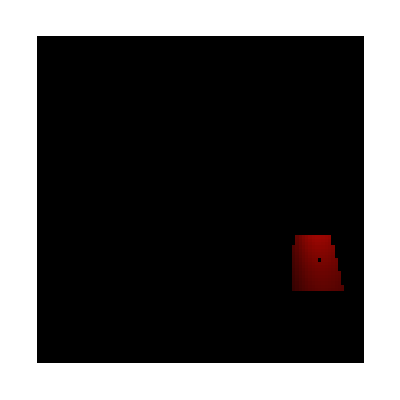

```mathematica
gPrint["Rendered Scene"];
ClearAll[scene,colorMul,imgTable];
scene=pbrtLoadScene["pbrtTestScene.scene"];
colorMul=10;
imgTable=pbrtRenderTile[{77,61},{93,77},scene,colorMul];
Show[ArrayPlot[imgTable]]
```

```mathematica
gPrint["Switch Scenes"];
ClearAll[scene,colorMul,imgTable,renderedFlag];
scene=pbrtLoadScene["pbrtTestScene.scene"];
colorMul=10;
imgTable=Table[1,scene["resx"],scene["resy"]];
renderedFlag=False;
Manipulate[
Show[
If[renderedFlag,
	ArrayPlot[imgTable],
	pbrtPlotOriginScene[scene]],

pbrtPlot3DOptions[scene]
],
Button["Rendered",renderedFlag=!renderedFlag],
Button["Start",imgTable=pbrtRenderTile[{77,61},{93,77},scene,colorMul]],
{{colorMul,10},1,20}
]
```

Switch Scenes

```mathematica
gPrint["Pixel Log"];
ClearAll[scene,l1,log1,l2,log2];
scene=pbrtLoadScene["pbrtTestScene.scene"];
l1=pbrtSamplerIntegratorRender[{51,12},scene,2];
log1=pbrtCurrPixelLog;
l2=pbrtSamplerIntegratorRender[{78,80},scene];
log2=pbrtCurrPixelLog;
pbrtLogPrintPixel[log1];
(*pbrtLogPrintPixel[log2];*)
```

Pixel Log

pixel

{51,12}

cameraRay

<|o→{278.,-800.,273.},d→{0.0105278,0.96919,0.246089}|>

bounce_0

-->base

<|index→0,rayo→{278.,-800.,273.},rayd→{0.0105278,0.96919,0.246089},le→{20.7467,10.8234,2.76459},leBeta→{1,1,1},ld→{0,0,0},ldBeta→{1,1,1},l→{20.7467,10.8234,2.76459}|>

-->misLight

<|l_wo→{-0.0105278,-0.96919,-0.246089},l_wi→{0,0,0},l_lightPdf→0,l_scatteringPdf→0,l_li→{0,0,0},l_f→{0,0,0},l_lo→{0,0,0}|>

-->misBsdf

<|b_wo→{-0.0105278,-0.96919,-0.246089},b_wi→{-0.141421,0.141421,-0.979796},b_lightPdf→0,b_scatteringPdf→0.311879,b_li→{0,0,0},b_f→{6.60389,3.44519,0.879996},b_tr→1,b_lo→{0,0,0}|>

-->nextBounce

<|next_rayo→{289.795,285.81,548.7},next_rayd→{-0.141421,0.141421,-0.979796},next_beta→{20.7467,10.8234,2.76459}|>

bounce_1

-->base

<|index→1,rayo→{289.795,285.81,548.7},rayd→{-0.141421,0.141421,-0.979796},le→{0,0,0},leBeta→{20.7467,10.8234,2.76459},ld→{0.123838,0.0507598,0.0124068},ldBeta→{20.7467,10.8234,2.76459},l→{2.56923,0.549393,0.0342998}|>

-->misLight

<|l_wo→{0.141421,-0.141421,0.979796},l_wi→{0.164726,-0.10134,0.98112},l_lightPdf→46.7091,l_scatteringPdf→0.3123,l_li→{20.7467,10.8234,2.76459},l_f→{0.282319,0.221816,0.212259},l_lo→{0.123024,0.0504262,0.0123253}|>

-->misBsdf

<|b_wo→{0.141421,-0.141421,0.979796},b_wi→{0.141421,-0.141421,0.979796},b_lightPdf→46.8987,b_scatteringPdf→0.311879,b_li→{20.7467,10.8234,2.76459},b_f→{0.282319,0.221816,0.212259},b_tr→1,b_lo→{0.000813713,0.000333532,0.0000815227}|>

-->nextBounce

<|next_rayo→{210.597,365.008,-1.90735×10^-6},next_rayd→{0.141421,-0.141421,0.979796},next_beta→{18.4009,7.54233,1.84352}|>

li

{23.316,11.3728,2.79889}

```mathematica
gPrint["Validate Pixel"];
ClearAll[scene,testData];
scene=pbrtLoadScene["pbrtTestScene.scene"];
testData=ToExpression[Import["pbrtTestData.pixels"]];
pbrtValidateSinglePixel[51,12,scene,testData]
```

Validate Pixel

{True,{20.7467,10.8234,2.76459},{20.7467,10.8234,2.76459}}

```mathematica
gPrint["Validate Tile"];
ClearAll[scene,testData];
scene=pbrtLoadScene["pbrtTestScene.scene"];
testData=ToExpression[Import["pbrtTestData.pixels"]];
pbrtValidateTilePixels[{45,0},{61,13},scene,testData]
(*pbrtValidateTilePixels[{45,0},{46,1},scene,testData]*)
```

Validate Tile

<|total→208,ok→208,fail→0,black→193|>

```mathematica
gPrint["Plot Path"];
ClearAll[scene,l,pixelLog];
scene=pbrtLoadScene["pbrtTestScene.scene"];
l=pbrtSamplerIntegratorRender[{51,12},scene,2];
pixelLog=pbrtCurrPixelLog;
(*pbrtLogPrintPixel[pixelLog];*)
pbrtPlotPath[scene,pixelLog]
```

Plot Path

{<|origin→{278.,-800.,273.},dir→{0.0105278,0.96919,0.246089},length→1120.33|>,<|origin→{289.795,285.81,548.7},dir→{-0.141421,0.141421,-0.979796},length→560.015|>,<|origin→{210.597,365.008,-1.90735×10^-6},dir→{0.141421,-0.141421,0.979796},length→100|>}

-Graphics3D-